## Nicolas’s Testing Ground

```mathematica
point1[x_]:=Module[{},
If[x≤5,{x,x},{x,10-x}]];
Animate[Graphics[Point[point1[t]],Axes->True,AspectRatio->Automatic, PlotRange->{{0,15},{0,15}}],{t,0,10}]
(*To Test animating an If statement*)
```

```mathematica
p=Plot[Sin[x],{x,-Pi,Pi}];
Animate[Show[p,Graphics[Point[{a,Sin[a]}]]],{a,-1,1}]
(*Suggestion given by the professor on how to format the combined plot and graphic. This one uses a Plot command though and not a parametric plot*)
```

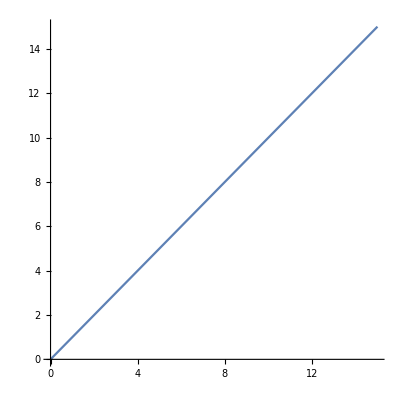

```mathematica
p2=ParametricPlot[{t,t},{t,0,15}]
Animate[Show[p2,Graphics[Point[{a,a}],Axes->True,AspectRatio->Automatic, PlotRange->{{0,15},{0,15}}]],{a,0,10}]
```

```mathematica
(*So it worked for a parametric plot. I'm guessing that there was a problem in the nesting of the two functions between Animate, Show, and Graphic
```